```mathematica
Clear["Global`*"]
```

```mathematica
m=Solve[-(I*△m+km)*m1-I*gma*a1+√(2km)*min+I*w*m1==0,m1];
mm=Solve[-(-I*△m+km)*m2+I*gma*a2+√(2km)*mlin+I*w*m2==0,m2];
a=Solve[-(I*△a+ka)*a1-I*gma*(m1/.m)+√(2*ka)*ain+I*g0*as*q+I*w*a1==0,a1];
aa=Solve[-(-I*△a+ka)*a2+I*gma*(m2/.mm)+√(2*ka)*alin-I*g0*als*q+I*w*a2==0,a2];
q1=Solve[{wb*p+I*w*q==0,-(wb+4*η)*q-rb*p+g0*(a1/.a)*als+g0*as*(a2/.aa)+ξ+I*w*p==0},{q,p}];
q/.q1
```

{-(wb (ξ-(√2 alin as g0 √ka)/(-ka+ⅈ w+ⅈ △a-gma^2/(km-ⅈ w-ⅈ △m))-(√2 ain als g0 √ka)/(-ka+ⅈ w-ⅈ △a-gma^2/(km-ⅈ w+ⅈ △m))-(ⅈ √2 as g0 gma √km mlin)/((-ka+ⅈ w+ⅈ △a-gma^2/(km-ⅈ w-ⅈ △m)) (km-ⅈ w-ⅈ △m))+(ⅈ √2 als g0 gma √km min)/((-ka+ⅈ w-ⅈ △a-gma^2/(km-ⅈ w+ⅈ △m)) (km-ⅈ w+ⅈ △m))))/(-ⅈ (-rb+ⅈ w) w+wb (-wb-4 η+(ⅈ als as g0^2)/(-ka+ⅈ w+ⅈ △a-gma^2/(km-ⅈ w-ⅈ △m))-(ⅈ als as g0^2)/(-ka+ⅈ w-ⅈ △a-gma^2/(km-ⅈ w+ⅈ △m))))}

```mathematica
Clear["Global`*"]
```

```mathematica
r=0.8;(*文章△a*)
△s=1Pi*10^4;
η=0wb;
△a=-50wb;(*文章△c*)
N1=Sinh[r]^2;
M1=Sinh[r]Cosh[r];
wb=1Pi*10^6;(*文章wm*)
ka=3.5*Pi*10^6;(*文章k*)
km=1.2*Pi*10^6;(*文章ra*)
rb=Pi;(*文章rm*)
ℏ=1.0546*10^(-34);

kB=1.380649*10^(-23);

T=10*10^(-3);

Nb=1/(Exp[(ℏ*wb)/(kB*T)]-1);
Nm=0;

g0=1600*Pi;
Ep=3.5*10^12;
as=(-I*Ep (km+ⅈ △m))/(gma^2+ka km-ⅈ g0 km qs+ⅈ km △a+ⅈ ka △m+g0 qs △m-△a △m);
als=(I*Ep (km-ⅈ △m))/(gma^2+ka km+ⅈ g0 km qs-ⅈ km △a-ⅈ ka △m+g0 qs △m-△a △m);
qs=(2 (g0 km^2 wb △a+4 g0 km^2 η △a-g0 gma^2 wb △m-4 g0 gma^2 η △m+g0 wb △a △m^2+4 g0 η △a △m^2))/(3 (g0^2 km^2 wb+4 g0^2 km^2 η+g0^2 wb △m^2+4 g0^2 η △m^2))-(2^(1/3) (-4 (g0 km^2 wb △a+4 g0 km^2 η △a-g0 gma^2 wb △m-4 g0 gma^2 η △m+g0 wb △a △m^2+4 g0 η △a △m^2)^2+3 (g0^2 km^2 wb+4 g0^2 km^2 η+g0^2 wb △m^2+4 g0^2 η △m^2) (gma^4 wb+2 gma^2 ka km wb+ka^2 km^2 wb+4 gma^4 η+8 gma^2 ka km η+4 ka^2 km^2 η+km^2 wb △a^2+4 km^2 η △a^2-2 gma^2 wb △a △m-8 gma^2 η △a △m+ka^2 wb △m^2+4 ka^2 η △m^2+wb △a^2 △m^2+4 η △a^2 △m^2)))/(3 (g0^2 km^2 wb+4 g0^2 km^2 η+g0^2 wb △m^2+4 g0^2 η △m^2) (27 Ep^2 g0^5 km^6 wb^2+216 Ep^2 g0^5 km^6 wb η+432 Ep^2 g0^5 km^6 η^2-18 g0^3 gma^4 km^4 wb^3 △a-36 g0^3 gma^2 ka km^5 wb^3 △a-18 g0^3 ka^2 km^6 wb^3 △a-216 g0^3 gma^4 km^4 wb^2 η △a-432 g0^3 gma^2 ka km^5 wb^2 η △a-216 g0^3 ka^2 km^6 wb^2 η △a-864 g0^3 gma^4 km^4 wb η^2 △a-1728 g0^3 gma^2 ka km^5 wb η^2 △a-864 g0^3 ka^2 km^6 wb η^2 △a-1152 g0^3 gma^4 km^4 η^3 △a-2304 g0^3 gma^2 ka km^5 η^3 △a-1152 g0^3 ka^2 km^6 η^3 △a-2 g0^3 km^6 wb^3 △a^3-24 g0^3 km^6 wb^2 η △a^3-96 g0^3 km^6 wb η^2 △a^3-128 g0^3 km^6 η^3 △a^3+18 g0^3 gma^6 km^2 wb^3 △m+36 g0^3 gma^4 ka km^3 wb^3 △m+18 g0^3 gma^2 ka^2 km^4 wb^3 △m+216 g0^3 gma^6 km^2 wb^2 η △m+432 g0^3 gma^4 ka km^3 wb^2 η △m+216 g0^3 gma^2 ka^2 km^4 wb^2 η △m+864 g0^3 gma^6 km^2 wb η^2 △m+1728 g0^3 gma^4 ka km^3 wb η^2 △m+864 g0^3 gma^2 ka^2 km^4 wb η^2 △m+1152 g0^3 gma^6 km^2 η^3 △m+2304 g0^3 gma^4 ka km^3 η^3 △m+1152 g0^3 gma^2 ka^2 km^4 η^3 △m+6 g0^3 gma^2 km^4 wb^3 △a^2 △m+72 g0^3 gma^2 km^4 wb^2 η △a^2 △m+288 g0^3 gma^2 km^4 wb η^2 △a^2 △m+384 g0^3 gma^2 km^4 η^3 △a^2 △m+81 Ep^2 g0^5 km^4 wb^2 △m^2+648 Ep^2 g0^5 km^4 wb η △m^2+1296 Ep^2 g0^5 km^4 η^2 △m^2-24 g0^3 gma^4 km^2 wb^3 △a △m^2-72 g0^3 gma^2 ka km^3 wb^3 △a △m^2-54 g0^3 ka^2 km^4 wb^3 △a △m^2-288 g0^3 gma^4 km^2 wb^2 η △a △m^2-864 g0^3 gma^2 ka km^3 wb^2 η △a △m^2-648 g0^3 ka^2 km^4 wb^2 η △a △m^2-1152 g0^3 gma^4 km^2 wb η^2 △a △m^2-3456 g0^3 gma^2 ka km^3 wb η^2 △a △m^2-2592 g0^3 ka^2 km^4 wb η^2 △a △m^2-1536 g0^3 gma^4 km^2 η^3 △a △m^2-4608 g0^3 gma^2 ka km^3 η^3 △a △m^2-3456 g0^3 ka^2 km^4 η^3 △a △m^2-6 g0^3 km^4 wb^3 △a^3 △m^2-72 g0^3 km^4 wb^2 η △a^3 △m^2-288 g0^3 km^4 wb η^2 △a^3 △m^2-384 g0^3 km^4 η^3 △a^3 △m^2+2 g0^3 gma^6 wb^3 △m^3+36 g0^3 gma^4 ka km wb^3 △m^3+36 g0^3 gma^2 ka^2 km^2 wb^3 △m^3+24 g0^3 gma^6 wb^2 η △m^3+432 g0^3 gma^4 ka km wb^2 η △m^3+432 g0^3 gma^2 ka^2 km^2 wb^2 η △m^3+96 g0^3 gma^6 wb η^2 △m^3+1728 g0^3 gma^4 ka km wb η^2 △m^3+1728 g0^3 gma^2 ka^2 km^2 wb η^2 △m^3+128 g0^3 gma^6 η^3 △m^3+2304 g0^3 gma^4 ka km η^3 △m^3+2304 g0^3 gma^2 ka^2 km^2 η^3 △m^3+12 g0^3 gma^2 km^2 wb^3 △a^2 △m^3+144 g0^3 gma^2 km^2 wb^2 η △a^2 △m^3+576 g0^3 gma^2 km^2 wb η^2 △a^2 △m^3+768 g0^3 gma^2 km^2 η^3 △a^2 △m^3+81 Ep^2 g0^5 km^2 wb^2 △m^4+648 Ep^2 g0^5 km^2 wb η △m^4+1296 Ep^2 g0^5 km^2 η^2 △m^4-6 g0^3 gma^4 wb^3 △a △m^4-36 g0^3 gma^2 ka km wb^3 △a △m^4-54 g0^3 ka^2 km^2 wb^3 △a △m^4-72 g0^3 gma^4 wb^2 η △a △m^4-432 g0^3 gma^2 ka km wb^2 η △a △m^4-648 g0^3 ka^2 km^2 wb^2 η △a △m^4-288 g0^3 gma^4 wb η^2 △a △m^4-1728 g0^3 gma^2 ka km wb η^2 △a △m^4-2592 g0^3 ka^2 km^2 wb η^2 △a △m^4-384 g0^3 gma^4 η^3 △a △m^4-2304 g0^3 gma^2 ka km η^3 △a △m^4-3456 g0^3 ka^2 km^2 η^3 △a △m^4-6 g0^3 km^2 wb^3 △a^3 △m^4-72 g0^3 km^2 wb^2 η △a^3 △m^4-288 g0^3 km^2 wb η^2 △a^3 △m^4-384 g0^3 km^2 η^3 △a^3 △m^4+18 g0^3 gma^2 ka^2 wb^3 △m^5+216 g0^3 gma^2 ka^2 wb^2 η △m^5+864 g0^3 gma^2 ka^2 wb η^2 △m^5+1152 g0^3 gma^2 ka^2 η^3 △m^5+6 g0^3 gma^2 wb^3 △a^2 △m^5+72 g0^3 gma^2 wb^2 η △a^2 △m^5+288 g0^3 gma^2 wb η^2 △a^2 △m^5+384 g0^3 gma^2 η^3 △a^2 △m^5+27 Ep^2 g0^5 wb^2 △m^6+216 Ep^2 g0^5 wb η △m^6+432 Ep^2 g0^5 η^2 △m^6-18 g0^3 ka^2 wb^3 △a △m^6-216 g0^3 ka^2 wb^2 η △a △m^6-864 g0^3 ka^2 wb η^2 △a △m^6-1152 g0^3 ka^2 η^3 △a △m^6-2 g0^3 wb^3 △a^3 △m^6-24 g0^3 wb^2 η △a^3 △m^6-96 g0^3 wb η^2 △a^3 △m^6-128 g0^3 η^3 △a^3 △m^6+√((27 Ep^2 g0^5 km^6 wb^2+216 Ep^2 g0^5 km^6 wb η+432 Ep^2 g0^5 km^6 η^2-18 g0^3 gma^4 km^4 wb^3 △a-36 g0^3 gma^2 ka km^5 wb^3 △a-18 g0^3 ka^2 km^6 wb^3 △a-216 g0^3 gma^4 km^4 wb^2 η △a-432 g0^3 gma^2 ka km^5 wb^2 η △a-216 g0^3 ka^2 km^6 wb^2 η △a-864 g0^3 gma^4 km^4 wb η^2 △a-1728 g0^3 gma^2 ka km^5 wb η^2 △a-864 g0^3 ka^2 km^6 wb η^2 △a-1152 g0^3 gma^4 km^4 η^3 △a-2304 g0^3 gma^2 ka km^5 η^3 △a-1152 g0^3 ka^2 km^6 η^3 △a-2 g0^3 km^6 wb^3 △a^3-24 g0^3 km^6 wb^2 η △a^3-96 g0^3 km^6 wb η^2 △a^3-128 g0^3 km^6 η^3 △a^3+18 g0^3 gma^6 km^2 wb^3 △m+36 g0^3 gma^4 ka km^3 wb^3 △m+18 g0^3 gma^2 ka^2 km^4 wb^3 △m+216 g0^3 gma^6 km^2 wb^2 η △m+432 g0^3 gma^4 ka km^3 wb^2 η △m+216 g0^3 gma^2 ka^2 km^4 wb^2 η △m+864 g0^3 gma^6 km^2 wb η^2 △m+1728 g0^3 gma^4 ka km^3 wb η^2 △m+864 g0^3 gma^2 ka^2 km^4 wb η^2 △m+1152 g0^3 gma^6 km^2 η^3 △m+2304 g0^3 gma^4 ka km^3 η^3 △m+1152 g0^3 gma^2 ka^2 km^4 η^3 △m+6 g0^3 gma^2 km^4 wb^3 △a^2 △m+72 g0^3 gma^2 km^4 wb^2 η △a^2 △m+288 g0^3 gma^2 km^4 wb η^2 △a^2 △m+384 g0^3 gma^2 km^4 η^3 △a^2 △m+81 Ep^2 g0^5 km^4 wb^2 △m^2+648 Ep^2 g0^5 km^4 wb η △m^2+1296 Ep^2 g0^5 km^4 η^2 △m^2-24 g0^3 gma^4 km^2 wb^3 △a △m^2-72 g0^3 gma^2 ka km^3 wb^3 △a △m^2-54 g0^3 ka^2 km^4 wb^3 △a △m^2-288 g0^3 gma^4 km^2 wb^2 η △a △m^2-864 g0^3 gma^2 ka km^3 wb^2 η △a △m^2-648 g0^3 ka^2 km^4 wb^2 η △a △m^2-1152 g0^3 gma^4 km^2 wb η^2 △a △m^2-3456 g0^3 gma^2 ka km^3 wb η^2 △a △m^2-2592 g0^3 ka^2 km^4 wb η^2 △a △m^2-1536 g0^3 gma^4 km^2 η^3 △a △m^2-4608 g0^3 gma^2 ka km^3 η^3 △a △m^2-3456 g0^3 ka^2 km^4 η^3 △a △m^2-6 g0^3 km^4 wb^3 △a^3 △m^2-72 g0^3 km^4 wb^2 η △a^3 △m^2-288 g0^3 km^4 wb η^2 △a^3 △m^2-384 g0^3 km^4 η^3 △a^3 △m^2+2 g0^3 gma^6 wb^3 △m^3+36 g0^3 gma^4 ka km wb^3 △m^3+36 g0^3 gma^2 ka^2 km^2 wb^3 △m^3+24 g0^3 gma^6 wb^2 η △m^3+432 g0^3 gma^4 ka km wb^2 η △m^3+432 g0^3 gma^2 ka^2 km^2 wb^2 η △m^3+96 g0^3 gma^6 wb η^2 △m^3+1728 g0^3 gma^4 ka km wb η^2 △m^3+1728 g0^3 gma^2 ka^2 km^2 wb η^2 △m^3+128 g0^3 gma^6 η^3 △m^3+2304 g0^3 gma^4 ka km η^3 △m^3+2304 g0^3 gma^2 ka^2 km^2 η^3 △m^3+12 g0^3 gma^2 km^2 wb^3 △a^2 △m^3+144 g0^3 gma^2 km^2 wb^2 η △a^2 △m^3+576 g0^3 gma^2 km^2 wb η^2 △a^2 △m^3+768 g0^3 gma^2 km^2 η^3 △a^2 △m^3+81 Ep^2 g0^5 km^2 wb^2 △m^4+648 Ep^2 g0^5 km^2 wb η △m^4+1296 Ep^2 g0^5 km^2 η^2 △m^4-6 g0^3 gma^4 wb^3 △a △m^4-36 g0^3 gma^2 ka km wb^3 △a △m^4-54 g0^3 ka^2 km^2 wb^3 △a △m^4-72 g0^3 gma^4 wb^2 η △a △m^4-432 g0^3 gma^2 ka km wb^2 η △a △m^4-648 g0^3 ka^2 km^2 wb^2 η △a △m^4-288 g0^3 gma^4 wb η^2 △a △m^4-1728 g0^3 gma^2 ka km wb η^2 △a △m^4-2592 g0^3 ka^2 km^2 wb η^2 △a △m^4-384 g0^3 gma^4 η^3 △a △m^4-2304 g0^3 gma^2 ka km η^3 △a △m^4-3456 g0^3 ka^2 km^2 η^3 △a △m^4-6 g0^3 km^2 wb^3 △a^3 △m^4-72 g0^3 km^2 wb^2 η △a^3 △m^4-288 g0^3 km^2 wb η^2 △a^3 △m^4-384 g0^3 km^2 η^3 △a^3 △m^4+18 g0^3 gma^2 ka^2 wb^3 △m^5+216 g0^3 gma^2 ka^2 wb^2 η △m^5+864 g0^3 gma^2 ka^2 wb η^2 △m^5+1152 g0^3 gma^2 ka^2 η^3 △m^5+6 g0^3 gma^2 wb^3 △a^2 △m^5+72 g0^3 gma^2 wb^2 η △a^2 △m^5+288 g0^3 gma^2 wb η^2 △a^2 △m^5+384 g0^3 gma^2 η^3 △a^2 △m^5+27 Ep^2 g0^5 wb^2 △m^6+216 Ep^2 g0^5 wb η △m^6+432 Ep^2 g0^5 η^2 △m^6-18 g0^3 ka^2 wb^3 △a △m^6-216 g0^3 ka^2 wb^2 η △a △m^6-864 g0^3 ka^2 wb η^2 △a △m^6-1152 g0^3 ka^2 η^3 △a △m^6-2 g0^3 wb^3 △a^3 △m^6-24 g0^3 wb^2 η △a^3 △m^6-96 g0^3 wb η^2 △a^3 △m^6-128 g0^3 η^3 △a^3 △m^6)^2+4 (-4 (g0 km^2 wb △a+4 g0 km^2 η △a-g0 gma^2 wb △m-4 g0 gma^2 η △m+g0 wb △a △m^2+4 g0 η △a △m^2)^2+3 (g0^2 km^2 wb+4 g0^2 km^2 η+g0^2 wb △m^2+4 g0^2 η △m^2) (gma^4 wb+2 gma^2 ka km wb+ka^2 km^2 wb+4 gma^4 η+8 gma^2 ka km η+4 ka^2 km^2 η+km^2 wb △a^2+4 km^2 η △a^2-2 gma^2 wb △a △m-8 gma^2 η △a △m+ka^2 wb △m^2+4 ka^2 η △m^2+wb △a^2 △m^2+4 η △a^2 △m^2))^3))^(1/3))+(27 Ep^2 g0^5 km^6 wb^2+216 Ep^2 g0^5 km^6 wb η+432 Ep^2 g0^5 km^6 η^2-18 g0^3 gma^4 km^4 wb^3 △a-36 g0^3 gma^2 ka km^5 wb^3 △a-18 g0^3 ka^2 km^6 wb^3 △a-216 g0^3 gma^4 km^4 wb^2 η △a-432 g0^3 gma^2 ka km^5 wb^2 η △a-216 g0^3 ka^2 km^6 wb^2 η △a-864 g0^3 gma^4 km^4 wb η^2 △a-1728 g0^3 gma^2 ka km^5 wb η^2 △a-864 g0^3 ka^2 km^6 wb η^2 △a-1152 g0^3 gma^4 km^4 η^3 △a-2304 g0^3 gma^2 ka km^5 η^3 △a-1152 g0^3 ka^2 km^6 η^3 △a-2 g0^3 km^6 wb^3 △a^3-24 g0^3 km^6 wb^2 η △a^3-96 g0^3 km^6 wb η^2 △a^3-128 g0^3 km^6 η^3 △a^3+18 g0^3 gma^6 km^2 wb^3 △m+36 g0^3 gma^4 ka km^3 wb^3 △m+18 g0^3 gma^2 ka^2 km^4 wb^3 △m+216 g0^3 gma^6 km^2 wb^2 η △m+432 g0^3 gma^4 ka km^3 wb^2 η △m+216 g0^3 gma^2 ka^2 km^4 wb^2 η △m+864 g0^3 gma^6 km^2 wb η^2 △m+1728 g0^3 gma^4 ka km^3 wb η^2 △m+864 g0^3 gma^2 ka^2 km^4 wb η^2 △m+1152 g0^3 gma^6 km^2 η^3 △m+2304 g0^3 gma^4 ka km^3 η^3 △m+1152 g0^3 gma^2 ka^2 km^4 η^3 △m+6 g0^3 gma^2 km^4 wb^3 △a^2 △m+72 g0^3 gma^2 km^4 wb^2 η △a^2 △m+288 g0^3 gma^2 km^4 wb η^2 △a^2 △m+384 g0^3 gma^2 km^4 η^3 △a^2 △m+81 Ep^2 g0^5 km^4 wb^2 △m^2+648 Ep^2 g0^5 km^4 wb η △m^2+1296 Ep^2 g0^5 km^4 η^2 △m^2-24 g0^3 gma^4 km^2 wb^3 △a △m^2-72 g0^3 gma^2 ka km^3 wb^3 △a △m^2-54 g0^3 ka^2 km^4 wb^3 △a △m^2-288 g0^3 gma^4 km^2 wb^2 η △a △m^2-864 g0^3 gma^2 ka km^3 wb^2 η △a △m^2-648 g0^3 ka^2 km^4 wb^2 η △a △m^2-1152 g0^3 gma^4 km^2 wb η^2 △a △m^2-3456 g0^3 gma^2 ka km^3 wb η^2 △a △m^2-2592 g0^3 ka^2 km^4 wb η^2 △a △m^2-1536 g0^3 gma^4 km^2 η^3 △a △m^2-4608 g0^3 gma^2 ka km^3 η^3 △a △m^2-3456 g0^3 ka^2 km^4 η^3 △a △m^2-6 g0^3 km^4 wb^3 △a^3 △m^2-72 g0^3 km^4 wb^2 η △a^3 △m^2-288 g0^3 km^4 wb η^2 △a^3 △m^2-384 g0^3 km^4 η^3 △a^3 △m^2+2 g0^3 gma^6 wb^3 △m^3+36 g0^3 gma^4 ka km wb^3 △m^3+36 g0^3 gma^2 ka^2 km^2 wb^3 △m^3+24 g0^3 gma^6 wb^2 η △m^3+432 g0^3 gma^4 ka km wb^2 η △m^3+432 g0^3 gma^2 ka^2 km^2 wb^2 η △m^3+96 g0^3 gma^6 wb η^2 △m^3+1728 g0^3 gma^4 ka km wb η^2 △m^3+1728 g0^3 gma^2 ka^2 km^2 wb η^2 △m^3+128 g0^3 gma^6 η^3 △m^3+2304 g0^3 gma^4 ka km η^3 △m^3+2304 g0^3 gma^2 ka^2 km^2 η^3 △m^3+12 g0^3 gma^2 km^2 wb^3 △a^2 △m^3+144 g0^3 gma^2 km^2 wb^2 η △a^2 △m^3+576 g0^3 gma^2 km^2 wb η^2 △a^2 △m^3+768 g0^3 gma^2 km^2 η^3 △a^2 △m^3+81 Ep^2 g0^5 km^2 wb^2 △m^4+648 Ep^2 g0^5 km^2 wb η △m^4+1296 Ep^2 g0^5 km^2 η^2 △m^4-6 g0^3 gma^4 wb^3 △a △m^4-36 g0^3 gma^2 ka km wb^3 △a △m^4-54 g0^3 ka^2 km^2 wb^3 △a △m^4-72 g0^3 gma^4 wb^2 η △a △m^4-432 g0^3 gma^2 ka km wb^2 η △a △m^4-648 g0^3 ka^2 km^2 wb^2 η △a △m^4-288 g0^3 gma^4 wb η^2 △a △m^4-1728 g0^3 gma^2 ka km wb η^2 △a △m^4-2592 g0^3 ka^2 km^2 wb η^2 △a △m^4-384 g0^3 gma^4 η^3 △a △m^4-2304 g0^3 gma^2 ka km η^3 △a △m^4-3456 g0^3 ka^2 km^2 η^3 △a △m^4-6 g0^3 km^2 wb^3 △a^3 △m^4-72 g0^3 km^2 wb^2 η △a^3 △m^4-288 g0^3 km^2 wb η^2 △a^3 △m^4-384 g0^3 km^2 η^3 △a^3 △m^4+18 g0^3 gma^2 ka^2 wb^3 △m^5+216 g0^3 gma^2 ka^2 wb^2 η △m^5+864 g0^3 gma^2 ka^2 wb η^2 △m^5+1152 g0^3 gma^2 ka^2 η^3 △m^5+6 g0^3 gma^2 wb^3 △a^2 △m^5+72 g0^3 gma^2 wb^2 η △a^2 △m^5+288 g0^3 gma^2 wb η^2 △a^2 △m^5+384 g0^3 gma^2 η^3 △a^2 △m^5+27 Ep^2 g0^5 wb^2 △m^6+216 Ep^2 g0^5 wb η △m^6+432 Ep^2 g0^5 η^2 △m^6-18 g0^3 ka^2 wb^3 △a △m^6-216 g0^3 ka^2 wb^2 η △a △m^6-864 g0^3 ka^2 wb η^2 △a △m^6-1152 g0^3 ka^2 η^3 △a △m^6-2 g0^3 wb^3 △a^3 △m^6-24 g0^3 wb^2 η △a^3 △m^6-96 g0^3 wb η^2 △a^3 △m^6-128 g0^3 η^3 △a^3 △m^6+√((27 Ep^2 g0^5 km^6 wb^2+216 Ep^2 g0^5 km^6 wb η+432 Ep^2 g0^5 km^6 η^2-18 g0^3 gma^4 km^4 wb^3 △a-36 g0^3 gma^2 ka km^5 wb^3 △a-18 g0^3 ka^2 km^6 wb^3 △a-216 g0^3 gma^4 km^4 wb^2 η △a-432 g0^3 gma^2 ka km^5 wb^2 η △a-216 g0^3 ka^2 km^6 wb^2 η △a-864 g0^3 gma^4 km^4 wb η^2 △a-1728 g0^3 gma^2 ka km^5 wb η^2 △a-864 g0^3 ka^2 km^6 wb η^2 △a-1152 g0^3 gma^4 km^4 η^3 △a-2304 g0^3 gma^2 ka km^5 η^3 △a-1152 g0^3 ka^2 km^6 η^3 △a-2 g0^3 km^6 wb^3 △a^3-24 g0^3 km^6 wb^2 η △a^3-96 g0^3 km^6 wb η^2 △a^3-128 g0^3 km^6 η^3 △a^3+18 g0^3 gma^6 km^2 wb^3 △m+36 g0^3 gma^4 ka km^3 wb^3 △m+18 g0^3 gma^2 ka^2 km^4 wb^3 △m+216 g0^3 gma^6 km^2 wb^2 η △m+432 g0^3 gma^4 ka km^3 wb^2 η △m+216 g0^3 gma^2 ka^2 km^4 wb^2 η △m+864 g0^3 gma^6 km^2 wb η^2 △m+1728 g0^3 gma^4 ka km^3 wb η^2 △m+864 g0^3 gma^2 ka^2 km^4 wb η^2 △m+1152 g0^3 gma^6 km^2 η^3 △m+2304 g0^3 gma^4 ka km^3 η^3 △m+1152 g0^3 gma^2 ka^2 km^4 η^3 △m+6 g0^3 gma^2 km^4 wb^3 △a^2 △m+72 g0^3 gma^2 km^4 wb^2 η △a^2 △m+288 g0^3 gma^2 km^4 wb η^2 △a^2 △m+384 g0^3 gma^2 km^4 η^3 △a^2 △m+81 Ep^2 g0^5 km^4 wb^2 △m^2+648 Ep^2 g0^5 km^4 wb η △m^2+1296 Ep^2 g0^5 km^4 η^2 △m^2-24 g0^3 gma^4 km^2 wb^3 △a △m^2-72 g0^3 gma^2 ka km^3 wb^3 △a △m^2-54 g0^3 ka^2 km^4 wb^3 △a △m^2-288 g0^3 gma^4 km^2 wb^2 η △a △m^2-864 g0^3 gma^2 ka km^3 wb^2 η △a △m^2-648 g0^3 ka^2 km^4 wb^2 η △a △m^2-1152 g0^3 gma^4 km^2 wb η^2 △a △m^2-3456 g0^3 gma^2 ka km^3 wb η^2 △a △m^2-2592 g0^3 ka^2 km^4 wb η^2 △a △m^2-1536 g0^3 gma^4 km^2 η^3 △a △m^2-4608 g0^3 gma^2 ka km^3 η^3 △a △m^2-3456 g0^3 ka^2 km^4 η^3 △a △m^2-6 g0^3 km^4 wb^3 △a^3 △m^2-72 g0^3 km^4 wb^2 η △a^3 △m^2-288 g0^3 km^4 wb η^2 △a^3 △m^2-384 g0^3 km^4 η^3 △a^3 △m^2+2 g0^3 gma^6 wb^3 △m^3+36 g0^3 gma^4 ka km wb^3 △m^3+36 g0^3 gma^2 ka^2 km^2 wb^3 △m^3+24 g0^3 gma^6 wb^2 η △m^3+432 g0^3 gma^4 ka km wb^2 η △m^3+432 g0^3 gma^2 ka^2 km^2 wb^2 η △m^3+96 g0^3 gma^6 wb η^2 △m^3+1728 g0^3 gma^4 ka km wb η^2 △m^3+1728 g0^3 gma^2 ka^2 km^2 wb η^2 △m^3+128 g0^3 gma^6 η^3 △m^3+2304 g0^3 gma^4 ka km η^3 △m^3+2304 g0^3 gma^2 ka^2 km^2 η^3 △m^3+12 g0^3 gma^2 km^2 wb^3 △a^2 △m^3+144 g0^3 gma^2 km^2 wb^2 η △a^2 △m^3+576 g0^3 gma^2 km^2 wb η^2 △a^2 △m^3+768 g0^3 gma^2 km^2 η^3 △a^2 △m^3+81 Ep^2 g0^5 km^2 wb^2 △m^4+648 Ep^2 g0^5 km^2 wb η △m^4+1296 Ep^2 g0^5 km^2 η^2 △m^4-6 g0^3 gma^4 wb^3 △a △m^4-36 g0^3 gma^2 ka km wb^3 △a △m^4-54 g0^3 ka^2 km^2 wb^3 △a △m^4-72 g0^3 gma^4 wb^2 η △a △m^4-432 g0^3 gma^2 ka km wb^2 η △a △m^4-648 g0^3 ka^2 km^2 wb^2 η △a △m^4-288 g0^3 gma^4 wb η^2 △a △m^4-1728 g0^3 gma^2 ka km wb η^2 △a △m^4-2592 g0^3 ka^2 km^2 wb η^2 △a △m^4-384 g0^3 gma^4 η^3 △a △m^4-2304 g0^3 gma^2 ka km η^3 △a △m^4-3456 g0^3 ka^2 km^2 η^3 △a △m^4-6 g0^3 km^2 wb^3 △a^3 △m^4-72 g0^3 km^2 wb^2 η △a^3 △m^4-288 g0^3 km^2 wb η^2 △a^3 △m^4-384 g0^3 km^2 η^3 △a^3 △m^4+18 g0^3 gma^2 ka^2 wb^3 △m^5+216 g0^3 gma^2 ka^2 wb^2 η △m^5+864 g0^3 gma^2 ka^2 wb η^2 △m^5+1152 g0^3 gma^2 ka^2 η^3 △m^5+6 g0^3 gma^2 wb^3 △a^2 △m^5+72 g0^3 gma^2 wb^2 η △a^2 △m^5+288 g0^3 gma^2 wb η^2 △a^2 △m^5+384 g0^3 gma^2 η^3 △a^2 △m^5+27 Ep^2 g0^5 wb^2 △m^6+216 Ep^2 g0^5 wb η △m^6+432 Ep^2 g0^5 η^2 △m^6-18 g0^3 ka^2 wb^3 △a △m^6-216 g0^3 ka^2 wb^2 η △a △m^6-864 g0^3 ka^2 wb η^2 △a △m^6-1152 g0^3 ka^2 η^3 △a △m^6-2 g0^3 wb^3 △a^3 △m^6-24 g0^3 wb^2 η △a^3 △m^6-96 g0^3 wb η^2 △a^3 △m^6-128 g0^3 η^3 △a^3 △m^6)^2+4 (-4 (g0 km^2 wb △a+4 g0 km^2 η △a-g0 gma^2 wb △m-4 g0 gma^2 η △m+g0 wb △a △m^2+4 g0 η △a △m^2)^2+3 (g0^2 km^2 wb+4 g0^2 km^2 η+g0^2 wb △m^2+4 g0^2 η △m^2) (gma^4 wb+2 gma^2 ka km wb+ka^2 km^2 wb+4 gma^4 η+8 gma^2 ka km η+4 ka^2 km^2 η+km^2 wb △a^2+4 km^2 η △a^2-2 gma^2 wb △a △m-8 gma^2 η △a △m+ka^2 wb △m^2+4 ka^2 η △m^2+wb △a^2 △m^2+4 η △a^2 △m^2))^3))^(1/3)/(3 2^(1/3) (g0^2 km^2 wb+4 g0^2 km^2 η+g0^2 wb △m^2+4 g0^2 η △m^2));
```

```mathematica
d1=(-ⅈ g0*qs-ka+ⅈ w+ⅈ △a-gma^2/(km-ⅈ w-ⅈ △m));
d2=(ⅈ g0*qs-ka+ⅈ w-ⅈ △a-gma^2/(km-ⅈ w+ⅈ △m));
d3=(-ka-ⅈ g0*qs+ⅈ w+ⅈ △a-gma^2/(km-ⅈ w-ⅈ △m)) (km-ⅈ w-ⅈ △m);
d4=(-ka+ⅈ g0*qs+ⅈ w-ⅈ △a-gma^2/(km-ⅈ w+ⅈ △m)) (km-ⅈ w+ⅈ △m);
d=-ⅈ (-rb+ⅈ w) w+wb (-wb-4 η+(ⅈ als as g0^2)/(-ka-ⅈ g0*qs+ⅈ w+ⅈ △a-gma^2/(km-ⅈ w-ⅈ △m))-(ⅈ als as g0^2)/(-ka+ⅈ g0*qs+ⅈ w-ⅈ △a-gma^2/(km-ⅈ w+ⅈ △m)));
```

```mathematica
A=(2g0^2*ka*as*als*N1)/(d*(d/.w->-w)*d1*(d2/.w->-w))+(2g0^2*ka*as*als*(N1+1))/(d*(d/.w->-w)*d2*(d1/.w->-w))+(2g0^2*gma^2*km*as*als*(Nm+1))/(d*(d/.w->-w)*d4*(d3/.w->-w))+(2g0^2*gma^2*km*as*als*Nm)/(d*(d/.w->-w)*d3*(d4/.w->-w))+(rb*(2Nb+1))/(d*(d/.w->-w));
B=(2g0^2*ka*als*als*M1)/(d*(d/.w->(2*△s-w))*d2*(d2/.w->(2*△s-w)));
C1=(2g0^2*ka*as*as*M1)/(d*(d/.w->(-2*△s-w))*d1*(d1/.w->(-2*△s-w)));
```

```mathematica
△mmax=6;
△m=k*0.1wb+0.7wb;
gmamax=6;
gma=h*wb+5wb;
For[n=1,n≤△mmax,n++,
For[j=1,j≤gmamax,j++,eq[n,j]=1/(2*Pi)*wb^2*(A+B+C1)]];
```

```mathematica
tab=Integrate[Table[eq[k,h],{k,1,△mmax},{h,1,gmamax}],{w,-∞,∞}]//Re;
tab[[1,2]]
```

0.523319

```mathematica
qq=Flatten[Table[{△m/wb,gma/wb,tab[[k,h]]},{k,1,△mmax},{h,1,gmamax}],1]
```

{{0.8,6,0.564613},{0.8,7,0.523319},{0.8,8,0.503325},{0.8,9,0.495161},{0.8,10,0.497005},{0.8,11,0.509615},{0.9,6,0.532181},{0.9,7,0.501628},{0.9,8,0.488431},{0.9,9,0.485429},{0.9,10,0.491486},{0.9,11,0.507536},{1.,6,0.508388},{1.,7,0.485699},{1.,8,0.477683},{1.,9,0.478738},{1.,10,0.48816},{1.,11,0.506962},{1.1,6,0.491123},{1.1,7,0.474246},{1.1,8,0.470223},{1.1,9,0.474498},{1.1,10,0.486626},{1.1,11,0.507638},{1.2,6,0.478939},{1.2,7,0.466359},{1.2,8,0.465431},{1.2,9,0.472274},{1.2,10,0.486589},{1.2,11,0.50938},{1.3,6,0.470832},{1.3,7,0.461386},{1.3,8,0.462851},{1.3,9,0.471747},{1.3,10,0.48783},{1.3,11,0.512056}}

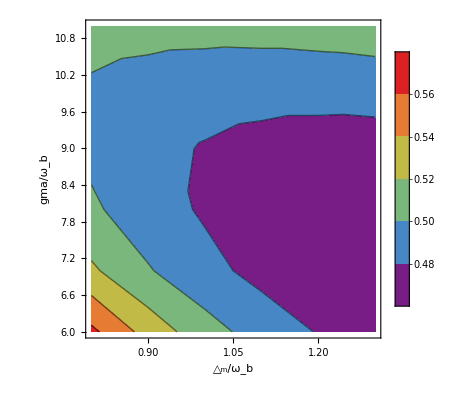

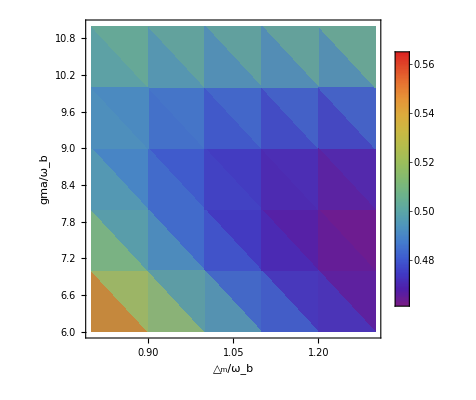

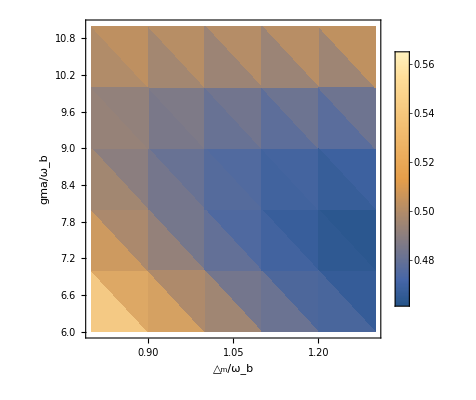

```mathematica
ListContourPlot[qq,PlotLegends->Automatic,ColorFunction->"Rainbow",PlotRange->All,Frame->True,FrameStyle->Directive[Black,18,Thin],PlotRange->Full,FrameLabel->{"△_m/ω_b","gma/ω_b"},LabelStyle->Directive[Black,15,Thick]]
ListDensityPlot[qq,PlotLegends->Automatic,ColorFunction->"Rainbow",PlotRange->All,Frame->True,FrameStyle->Directive[Black,18,Thin],PlotRange->Full,FrameLabel->{"△_m/ω_b","gma/ω_b"},LabelStyle->Directive[Black,15,Thick]]
ListDensityPlot[qq,PlotLegends->Automatic,PlotRange->All,Frame->True,FrameStyle->Directive[Black,18,Thin],PlotRange->Full,FrameLabel->{"△_m/ω_b","gma/ω_b"},LabelStyle->Directive[Black,15,Thick]]
```